```mathematica
genAll[w_,h_]:=Module[{width=w,height=h},
ucoords= NestList[#+RandomChoice[{-1,0,1}]&,1,w]

]
```

```mathematica
genAll[80,20]
```

{{1,1,0,-1,-1,0,-1,0,0,0,-1,-1,-2,-2,-1,-2,-1,-2,-1,-1,-1,0,0,-1,-2,-3,-2,-2,-2,-2,-3,-3,-2,-3,-3,-4,-5,-5,-4,-3,-2,-2,-1,0,1,2,1,2,3,3,2,3,4,5,5,4,3,2,3,4,4,3,2,2,2,3,2,1,1,0,0,-1,-1,-2,-1,-1,0,1,1,2,1},{1,0,-1,-1,-1,-2,-3,-4,-4,-4,-3,-2,-3,-2,-1,-2,-3,-2,-3,-2,-2,-3,-4,-4,-5,-6,-6,-5,-6,-7,-6,-6,-5,-5,-6,-5,-5,-4,-4,-4,-4,-3,-3,-2,-2,-3,-3,-2,-3,-2,-3,-3,-3,-3,-4,-3,-4,-4,-5,-5,-5,-5,-6,-7,-8,-7,-7,-6,-7,-8,-7,-6,-7,-7,-7,-8,-9,-10,-9,-8,-9},{1,2,2,3,4,3,2,2,1,0,-1,0,1,2,3,2,1,1,0,-1,0,-1,0,-1,0,-1,0,0,0,1,0,-1,-2,-2,-3,-2,-1,-1,0,1,2,1,2,3,4,4,4,4,3,2,2,1,2,3,4,5,5,5,6,5,5,5,4,3,4,4,5,5,4,5,4,3,3,3,2,2,1,2,2,1,1},{1,0,-1,-1,-1,-2,-1,-2,-3,-4,-4,-4,-4,-3,-2,-1,-2,-1,-2,-1,-1,-2,-3,-4,-4,-3,-3,-4,-4,-4,-4,-3,-4,-5,-5,-6,-6,-5,-6,-6,-5,-5,-5,-6,-6,-7,-8,-9,-8,-8,-9,-9,-8,-9,-10,-11,-12,-13,-14,-14,-14,-14,-15,-16,-17,-16,-16,-15,-14,-14,-15,-15,-16,-16,-17,-18,-19,-20,-20,-19,-20},{1,0,1,1,1,0,-1,-2,-3,-2,-3,-2,-2,-3,-4,-4,-4,-4,-3,-4,-4,-5,-4,-4,-3,-2,-1,-1,-2,-2,-1,-1,-2,-3,-3,-2,-3,-2,-2,-3,-2,-2,-3,-2,-1,-1,-1,-2,-1,-1,-1,0,0,0,0,-1,0,-1,-1,-1,-1,-2,-1,-1,-2,-3,-3,-3,-3,-2,-3,-3,-4,-5,-6,-5,-6,-7,-7,-6,-5},{1,2,3,4,4,4,3,3,4,5,4,4,3,2,3,4,4,3,2,2,2,1,1,1,2,3,4,5,5,6,7,8,8,8,7,7,7,7,8,7,6,6,5,4,4,4,3,2,1,1,0,0,-1,-2,-2,-3,-3,-3,-3,-4,-4,-4,-4,-3,-3,-4,-4,-4,-5,-6,-7,-8,-8,-8,-8,-9,-9,-8,-8,-9,-9},{1,0,0,1,2,3,3,3,4,3,4,5,6,5,5,6,6,7,8,8,9,8,9,8,7,7,7,6,7,6,7,6,7,6,7,7,8,8,9,8,9,10,10,9,8,7,6,6,7,7,6,7,6,6,7,6,5,4,3,4,3,4,4,4,5,5,5,4,4,4,5,6,5,5,4,3,3,4,5,6,5},{1,2,1,0,0,1,0,-1,0,1,0,-1,-2,-1,0,0,0,0,0,1,2,1,2,2,3,3,3,2,2,2,3,4,3,3,2,1,2,2,2,3,4,3,2,2,3,3,2,3,2,1,2,1,0,1,0,0,-1,-1,-1,0,0,0,-1,-2,-3,-4,-5,-5,-5,-5,-6,-7,-6,-5,-6,-5,-5,-6,-6,-5,-5},{1,1,0,-1,0,0,-1,-1,-2,-2,-2,-2,-3,-2,-3,-2,-1,-1,0,1,1,0,1,1,1,0,1,2,3,2,2,1,0,1,2,3,4,3,3,4,5,5,4,4,5,5,6,5,5,5,5,4,5,5,5,6,6,6,7,6,6,6,5,5,5,6,6,7,8,8,9,10,11,11,12,12,11,12,13,14,13},{1,1,0,0,0,1,0,1,0,0,1,1,1,0,-1,-1,-2,-2,-1,0,0,-1,0,-1,-2,-1,-2,-2,-1,0,1,2,2,3,4,5,5,5,4,4,4,4,4,5,6,6,5,4,4,3,3,3,2,2,1,1,2,1,2,2,1,0,1,2,1,1,0,0,0,0,0,0,-1,-1,-2,-1,-1,-2,-2,-1,0},{1,1,2,1,2,3,3,3,4,3,3,3,4,5,4,5,6,6,6,7,6,7,8,7,8,8,9,10,10,10,9,8,8,7,8,9,10,9,8,7,7,7,8,8,7,6,6,7,7,8,9,10,11,12,13,14,15,14,15,14,13,13,13,14,15,14,13,13,12,13,12,12,13,12,13,14,15,16,17,17,16},{1,1,0,0,-1,0,0,1,2,3,4,4,3,3,4,4,3,2,3,4,3,3,3,4,4,5,4,4,5,4,3,3,3,2,1,1,1,0,-1,-2,-1,0,0,-1,-2,-3,-2,-2,-3,-3,-4,-3,-4,-4,-5,-6,-6,-5,-5,-6,-7,-8,-8,-9,-8,-9,-10,-10,-9,-9,-8,-7,-7,-6,-5,-5,-5,-6,-5,-4,-3},{1,2,3,3,2,2,2,1,1,2,3,4,4,4,4,5,4,5,6,6,6,5,4,4,4,3,4,4,5,5,5,6,5,4,4,5,5,4,4,5,4,4,3,2,2,1,1,2,1,1,2,2,1,0,0,0,1,2,2,3,2,2,3,2,2,3,3,3,2,1,0,1,0,-1,0,1,0,1,0,1,0},{1,0,0,-1,-2,-2,-3,-2,-1,0,0,1,1,2,3,4,5,5,6,5,4,3,2,3,2,3,2,1,0,-1,0,1,2,3,3,4,5,5,6,6,6,5,6,6,5,6,7,7,8,7,6,7,6,5,5,5,6,6,6,7,7,8,7,7,7,7,7,8,7,7,7,7,7,8,7,7,8,7,8,7,8},{1,0,0,0,-1,-2,-3,-3,-2,-1,-2,-2,-3,-4,-3,-3,-4,-4,-4,-5,-5,-4,-5,-6,-5,-5,-4,-4,-5,-4,-3,-4,-5,-6,-6,-7,-8,-9,-9,-8,-9,-9,-8,-8,-9,-9,-9,-10,-10,-10,-9,-8,-7,-7,-7,-6,-7,-6,-7,-7,-8,-8,-8,-8,-7,-8,-9,-9,-9,-8,-8,-8,-9,-8,-9,-10,-10,-9,-9,-8,-8},{1,0,-1,-1,-1,-1,0,1,2,2,1,2,1,2,2,3,2,3,4,5,5,6,6,7,8,7,6,7,6,7,6,7,8,9,8,7,7,7,7,6,6,5,6,6,6,6,5,6,5,5,6,7,7,8,9,10,9,9,10,9,9,8,8,8,9,8,7,6,5,5,6,5,5,6,6,6,5,6,7,7,8},{1,2,2,3,3,2,3,2,2,3,4,5,4,4,5,6,6,5,4,5,5,4,4,5,6,7,7,6,7,6,5,5,4,5,6,5,6,6,7,8,9,8,9,10,9,9,8,7,8,8,9,9,9,10,9,8,9,8,8,9,8,8,9,10,10,11,11,11,10,10,10,10,10,9,8,8,7,8,9,9,9},{1,1,0,0,-1,0,-1,-1,-1,-1,0,-1,0,0,1,1,2,3,2,2,3,4,3,3,2,3,2,1,0,1,2,1,1,0,1,0,1,2,2,1,0,-1,0,0,-1,-1,0,0,-1,-2,-3,-4,-5,-5,-6,-5,-5,-6,-7,-8,-9,-9,-10,-10,-10,-10,-11,-11,-12,-13,-13,-12,-12,-12,-12,-13,-14,-14,-15,-14,-15},{1,2,1,2,2,3,4,4,5,5,6,7,8,9,8,9,9,8,9,8,8,8,9,9,8,9,10,9,8,9,8,8,9,10,11,10,9,9,10,9,8,8,8,7,6,6,6,7,7,7,7,8,9,10,11,11,11,10,10,10,9,10,10,9,10,10,11,12,12,12,13,13,12,11,11,10,11,11,12,13,12},{1,2,3,2,2,3,4,3,3,4,3,2,1,2,2,3,3,3,2,3,2,3,2,3,3,4,5,5,4,5,5,6,5,5,6,7,6,7,8,8,9,8,9,9,9,9,10,11,11,10,9,10,9,9,9,8,8,7,6,6,5,4,3,4,3,2,1,2,1,2,1,0,0,1,1,0,1,0,1,0,-1}}

```mathematica
VectorPlot[{x,y},{x,80},{y,20}]
```

```mathematica
NestList[Sqrt,256,3]
```

{256,16,4,2}

```mathematica
ucoords= NestList[#+RandomChoice[{-1,0,1}]&,1,8]
```

{1,0,0,-1,0,1,1,2,2}

```mathematica
vcoords= NestList[#+RandomChoice[{-1,0,1}]&,1,8]
```

{1,1,1,1,1,2,3,4,4}

```mathematica
uvcoords=Partition[ Riffle[ucoords,vcoords],2]
```

{{1,1},{0,1},{0,1},{-1,1},{0,1},{1,2},{1,3},{2,4},{2,4}}

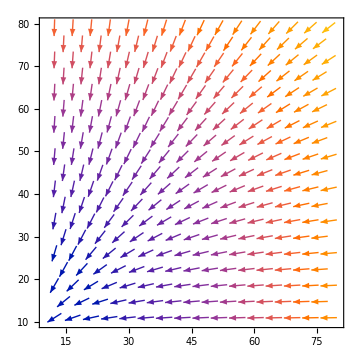

```mathematica
VectorPlot[{-x-x^2,-y-0.75y^2},{x,10,80},{y,10,80}]
```

```mathematica
liftCalcs=Last/@Partition[SortBy[{{5,0.,-37.5,7690.9080478578335},{6,0.,-37.5,10986.579154244446},{7,0.,-37.5,14855.887532339882},{8,0.,-37.5,19125.225886754015},{9,0.,-37.5,24216.58365113536},{10,0.,-37.5,29725.710117961975},{11,0.,-37.5,36768.909616569064},{12,0.,-37.5,44951.70162163475},{13,0.,-37.5,53175.903555982986},{14,0.,-37.5,63384.39276288201},{15,0.,-37.5,71821.5885000468},{16,0.,-37.5,80731.09925245988},{17,0.,-37.5,90953.97969595474},{18,0.,-37.5,100106.37184044522},{19,0.,-37.5,109977.68260392032},{20,0.,-37.5,119316.12153186541},{5,0.,-40.,8070.4890729728995},{6,0.,-40.,11556.002937912152},{7,0.,-40.,15640.189461491736},{8,0.,-40.,20169.06254612769},{9,0.,-40.,25541.863955030174},{10,0.,-40.,31398.820217047814},{11,0.,-40.,38670.10420912719},{12,0.,-40.,46826.01009327227},{13,0.,-40.,55434.01258290786},{14,0.,-40.,66569.13458573453},{15,0.,-40.,76585.10671786475},{16,0.,-40.,86768.87041498173},{17,0.,-40.,99210.59879769817},{18,0.,-40.,110351.4821983909},{19,0.,-40.,122221.2405285608},{20,0.,-40.,134972.03159817384},{5,0.,-42.5,8479.940742372672},{6,0.,-42.5,12136.586622061179},{7,0.,-42.5,16450.09570609943},{8,0.,-42.5,21268.942417138125},{9,0.,-42.5,26931.664624277542},{10,0.,-42.5,33028.341781109746},{11,0.,-42.5,40309.4900505039},{12,0.,-42.5,48040.4981767109},{13,0.,-42.5,56541.71201955595},{14,0.,-42.5,67594.33783977924},{15,0.,-42.5,78133.2412287709},{16,0.,-42.5,89222.79472519118},{17,0.,-42.5,102952.41679562822},{18,0.,-42.5,115956.41199700069},{19,0.,-42.5,129431.22008873812},{20,0.,-42.5,146232.6588107038},{5,0.,-45.,9340.701452423125},{6,0.,-45.,13326.427802258175},{7,0.,-45.,18067.823127370433},{8,0.,-45.,23448.311011105732},{9,0.,-45.,29711.439258882852},{10,0.,-45.,36445.38688926392},{11,0.,-45.,44347.84570474685},{12,0.,-45.,52388.367054609545},{13,0.,-45.,61417.5581098037},{14,0.,-45.,72610.57340287427},{15,0.,-45.,83796.82690943728},{16,0.,-45.,95833.88728879046},{17,0.,-45.,110687.03734001823},{18,0.,-45.,124960.33929709399},{19,0.,-45.,139944.93926824152},{20,0.,-45.,161269.84171434172},{5,0.,-47.5,10462.391370851168},{6,0.,-47.5,14875.923369033218},{7,0.,-47.5,20156.164735925886},{8,0.,-47.5,26284.63512714993},{9,0.,-47.5,33349.128341636046},{10,0.,-47.5,41010.988924123456},{11,0.,-47.5,49925.15316282669},{12,0.,-47.5,58818.19010580884},{13,0.,-47.5,69262.42872084065},{14,0.,-47.5,81518.30766594218},{15,0.,-47.5,94531.9210717397},{16,0.,-47.5,108838.3277660333},{17,0.,-47.5,126153.13049768009},{18,0.,-47.5,142998.91323972767},{19,0.,-47.5,160247.7771190268},{20,0.,-47.5,186095.8028011994},{5,0.,-50.,11129.452319075688},{6,0.,-50.,15840.81575775623},{7,0.,-50.,21509.56590459768},{8,0.,-50.,28270.389156730256},{9,0.,-50.,35989.05512107219},{10,0.,-50.,44517.16715130487},{11,0.,-50.,54488.79069227722},{12,0.,-50.,64410.45503942194},{13,0.,-50.,76656.13792470738},{14,0.,-50.,90294.55280409339},{15,0.,-50.,105593.45560395124},{16,0.,-50.,122168.69514341053},{17,0.,-50.,141996.9741219979},{18,0.,-50.,160730.11153568054},{19,0.,-50.,179002.0499688865},{20,0.,-50.,207187.61621214778},{5,0.,-52.5,12031.271563079299},{6,0.,-52.5,17162.16250140151},{7,0.,-52.5,23401.778556991383},{8,0.,-52.5,31109.38541457054},{9,0.,-52.5,39846.51365057017},{10,0.,-52.5,49639.469821668565},{11,0.,-52.5,61171.15368476646},{12,0.,-52.5,73011.70847234003},{13,0.,-52.5,87897.25108630882},{14,0.,-52.5,103768.55806571367},{15,0.,-52.5,122107.4401581288},{16,0.,-52.5,141330.5312303601},{17,0.,-52.5,163972.23696280972},{18,0.,-52.5,184521.77244427492},{19,0.,-52.5,203455.72377958143},{20,0.,-52.5,232600.2423153039},{5,2.5,-37.5,6682.252860430743},{6,2.5,-37.5,9622.319726490256},{7,2.5,-37.5,13164.516643261666},{8,2.5,-37.5,17121.163991295973},{9,2.5,-37.5,21975.959448018093},{10,2.5,-37.5,27276.984674419844},{11,2.5,-37.5,33659.54249719373},{12,2.5,-37.5,40514.59522292206},{13,2.5,-37.5,47140.29414379243},{14,2.5,-37.5,55995.65139705674},{15,2.5,-37.5,62725.70607806583},{16,2.5,-37.5,70730.46355538077},{17,2.5,-37.5,79251.22775678625},{18,2.5,-37.5,87292.82056938586},{19,2.5,-37.5,95784.06520450056},{20,2.5,-37.5,102686.30230990509},{5,2.5,-40.,7469.995390789545},{6,2.5,-40.,10727.83304149289},{7,2.5,-40.,14662.02775767612},{8,2.5,-40.,19174.298781618083},{9,2.5,-40.,24719.12204895648},{10,2.5,-40.,30945.71273501346},{11,2.5,-40.,38338.92270304813},{12,2.5,-40.,46065.996113070614},{13,2.5,-40.,53475.46275164213},{14,2.5,-40.,63354.34883774574},{15,2.5,-40.,71369.68890616356},{16,2.5,-40.,79917.91142916781},{17,2.5,-40.,89985.32620362236},{18,2.5,-40.,98875.89064017158},{19,2.5,-40.,108573.27520158282},{20,2.5,-40.,117588.18143492294},{5,2.5,-42.5,7827.3619908544515},{6,2.5,-42.5,11288.341530651458},{7,2.5,-42.5,15511.361560906978},{8,2.5,-42.5,20412.45785220546},{9,2.5,-42.5,26379.24437440811},{10,2.5,-42.5,33056.58465880699},{11,2.5,-42.5,40881.92342881312},{12,2.5,-42.5,49076.47643505287},{13,2.5,-42.5,57312.999586389094},{14,2.5,-42.5,68211.55688982918},{15,2.5,-42.5,77696.77327988984},{16,2.5,-42.5,87532.87024324836},{17,2.5,-42.5,99382.42293171902},{18,2.5,-42.5,109972.52828872981},{19,2.5,-42.5,121011.61744243727},{20,2.5,-42.5,133309.68632694875},{5,2.5,-45.,8138.641166578313},{6,2.5,-45.,11744.404648331289},{7,2.5,-45.,16169.141714134606},{8,2.5,-45.,21283.216924261207},{9,2.5,-45.,27332.827433148133},{10,2.5,-45.,33985.540158737895},{11,2.5,-45.,41783.71333341904},{12,2.5,-45.,49903.24615820101},{13,2.5,-45.,58617.893297853705},{14,2.5,-45.,69939.16147072976},{15,2.5,-45.,80466.1417128363},{16,2.5,-45.,91775.53520983076},{17,2.5,-45.,105207.58072351235},{18,2.5,-45.,117635.93001274033},{19,2.5,-45.,130153.00630257535},{20,2.5,-45.,146473.70768380762},{5,2.5,-47.5,8822.38482849689},{6,2.5,-47.5,12745.682848931887},{7,2.5,-47.5,17522.975782119887},{8,2.5,-47.5,23006.276697873887},{9,2.5,-47.5,29259.395519652124},{10,2.5,-47.5,36010.07407635552},{11,2.5,-47.5,44012.47506301652},{12,2.5,-47.5,52136.81241052093},{13,2.5,-47.5,61473.567772987466},{14,2.5,-47.5,72979.30107310088},{15,2.5,-47.5,84333.02186141157},{16,2.5,-47.5,96875.39944861078},{17,2.5,-47.5,111617.73063758088},{18,2.5,-47.5,125310.52836459575},{19,2.5,-47.5,139113.46443087148},{20,2.5,-47.5,159584.0211977252},{5,2.5,-50.,10031.91968550744},{6,2.5,-50.,14411.0503251423},{7,2.5,-50.,19685.771213281827},{8,2.5,-50.,25778.46986324578},{9,2.5,-50.,32519.741628998177},{10,2.5,-50.,39920.19027348715},{11,2.5,-50.,48851.54612798533},{12,2.5,-50.,57788.8951083673},{13,2.5,-50.,68545.25634348023},{14,2.5,-50.,80933.97863171106},{15,2.5,-50.,93923.84307951247},{16,2.5,-50.,108347.29580262463},{17,2.5,-50.,125178.37100762909},{18,2.5,-50.,141084.97735415708},{19,2.5,-50.,156798.4226998044},{20,2.5,-50.,181545.36034947302},{5,2.5,-52.5,10580.097601077845},{6,2.5,-52.5,15116.745256147642},{7,2.5,-52.5,20551.5333248969},{8,2.5,-52.5,26956.77696135502},{9,2.5,-52.5,33951.7587761413},{10,2.5,-52.5,41984.405342220605},{11,2.5,-52.5,51831.47236134513},{12,2.5,-52.5,61537.64119377994},{13,2.5,-52.5,73661.62602696886},{14,2.5,-52.5,86852.30302720069},{15,2.5,-52.5,101680.83058512917},{16,2.5,-52.5,117795.93557421972},{17,2.5,-52.5,136670.07685302955},{18,2.5,-52.5,154150.4082538355},{19,2.5,-52.5,170905.91911942867},{20,2.5,-52.5,198130.51141820155},{5,5.,-37.5,6126.09929301827},{6,5.,-37.5,8863.521078881358},{7,5.,-37.5,12185.028870751294},{8,5.,-37.5,15802.149640306532},{9,5.,-37.5,20236.4934596808},{10,5.,-37.5,24997.23231488164},{11,5.,-37.5,30469.44351761671},{12,5.,-37.5,36349.68687277689},{13,5.,-37.5,41947.19988294451},{14,5.,-37.5,50073.256058698156},{15,5.,-37.5,55795.83192082641},{16,5.,-37.5,63471.57732043857},{17,5.,-37.5,71082.26016265718},{18,5.,-37.5,78513.61339516474},{19,5.,-37.5,86334.53118173692},{20,5.,-37.5,91923.88125105224},{5,5.,-40.,6819.551647843508},{6,5.,-40.,9859.243411729718},{7,5.,-40.,13537.635153292023},{8,5.,-40.,17649.014646072785},{9,5.,-40.,22568.760488070748},{10,5.,-40.,27876.434636244794},{11,5.,-40.,34051.33283517063},{12,5.,-40.,40621.48366898384},{13,5.,-40.,46881.475472640406},{14,5.,-40.,55722.51653819237},{15,5.,-40.,62317.93378581155},{16,5.,-40.,70205.0460025267},{17,5.,-40.,78868.6677361466},{18,5.,-40.,86809.44376636205},{19,5.,-40.,95614.4457291003},{20,5.,-40.,102329.32640875336},{5,5.,-42.5,7611.001371762483},{6,5.,-42.5,11041.008749453502},{7,5.,-42.5,15224.57401730814},{8,5.,-42.5,19955.572764573957},{9,5.,-42.5,25484.168342174795},{10,5.,-42.5,31473.203599928875},{11,5.,-42.5,38373.02903349282},{12,5.,-42.5,45640.166634709574},{13,5.,-42.5,52571.26295941318},{14,5.,-42.5,62225.382909795255},{15,5.,-42.5,69895.03560175063},{16,5.,-42.5,78296.41430506445},{17,5.,-42.5,88220.67187229617},{18,5.,-42.5,97055.88734746577},{19,5.,-42.5,106702.7836882298},{20,5.,-42.5,115655.52437209756},{5,5.,-45.,8210.877955009259},{6,5.,-45.,11977.711225857398},{7,5.,-45.,16578.354838357573},{8,5.,-45.,21778.778748198027},{9,5.,-45.,27744.275903082387},{10,5.,-45.,34232.54854116929},{11,5.,-45.,41666.13210781112},{12,5.,-45.,49464.19154471433},{13,5.,-45.,57259.50193315522},{14,5.,-45.,67810.06116141047},{15,5.,-45.,76790.20324637186},{16,5.,-45.,86547.0286892896},{17,5.,-45.,97886.01906698837},{18,5.,-45.,108061.1224490569},{19,5.,-45.,118436.16499175056},{20,5.,-45.,130573.1682601737},{5,5.,-47.5,8706.906119512414},{6,5.,-47.5,12696.900422363142},{7,5.,-47.5,17548.458600668753},{8,5.,-47.5,23056.58018949649},{9,5.,-47.5,29308.962966843435},{10,5.,-47.5,36118.11873446978},{11,5.,-47.5,43984.678176303474},{12,5.,-47.5,51987.906487862216},{13,5.,-47.5,60526.768896387126},{14,5.,-47.5,71485.7054920089},{15,5.,-47.5,81501.80344839909},{16,5.,-47.5,92640.79776427962},{17,5.,-47.5,105422.2573236663},{18,5.,-47.5,116893.20781238972},{19,5.,-47.5,128266.19945764505},{20,5.,-47.5,144293.37654974076},{5,5.,-50.,9575.709076590683},{6,5.,-50.,13960.69624825826},{7,5.,-50.,19253.971645538888},{8,5.,-50.,25329.41488728683},{9,5.,-50.,32118.939967553386},{10,5.,-50.,39479.75114018534},{11,5.,-50.,47888.04794638614},{12,5.,-50.,55781.88765542199},{13,5.,-50.,64842.99347646552},{14,5.,-50.,75992.17237263375},{15,5.,-50.,87143.47249185124},{16,5.,-50.,99862.58790972232},{17,5.,-50.,114354.0604546146},{18,5.,-50.,127504.79674430394},{19,5.,-50.,140379.2878454356},{20,5.,-50.,160599.35848007072},{5,5.,-52.5,10896.951566957741},{6,5.,-52.5,15827.389309028818},{7,5.,-52.5,21730.871157889072},{8,5.,-52.5,28604.347671247342},{9,5.,-52.5,36123.44734243606},{10,5.,-52.5,44224.97087609022},{11,5.,-52.5,52944.59869906232},{12,5.,-52.5,60526.822368028355},{13,5.,-52.5,70521.89281677456},{14,5.,-52.5,82589.81376146828},{15,5.,-52.5,95703.57627685228},{16,5.,-52.5,110314.53138352394},{17,5.,-52.5,126977.82425533466},{18,5.,-52.5,142413.53285940725},{19,5.,-52.5,157370.39063509103},{20,5.,-52.5,182029.53617379235},{5,7.5,-37.5,5604.902039005643},{6,7.5,-37.5,8070.453164474159},{7,7.5,-37.5,11060.376267017593},{8,7.5,-37.5,14259.184499129851},{9,7.5,-37.5,18223.750905418277},{10,7.5,-37.5,22511.406639803656},{11,7.5,-37.5,27302.801137907016},{12,7.5,-37.5,32386.777345814735},{13,7.5,-37.5,37056.38606051021},{14,7.5,-37.5,44379.55790138472},{15,7.5,-37.5,49138.43820592425},{16,7.5,-37.5,56411.52466900535},{17,7.5,-37.5,63069.299251102646},{18,7.5,-37.5,69845.54060453897},{19,7.5,-37.5,77127.93721909984},{20,7.5,-37.5,81668.419275899},{5,7.5,-40.,6194.6056559667095},{6,7.5,-40.,8961.992230959428},{7,7.5,-40.,12299.879182569617},{8,7.5,-40.,15946.631193515856},{9,7.5,-40.,20325.655107356863},{10,7.5,-40.,25029.912713040052},{11,7.5,-40.,30366.00760336769},{12,7.5,-40.,36099.96964017726},{13,7.5,-40.,41455.568468394515},{14,7.5,-40.,49562.98489461531},{15,7.5,-40.,55146.200121797905},{16,7.5,-40.,62682.75044164425},{17,7.5,-40.,70303.18607847943},{18,7.5,-40.,77424.18913987749},{19,7.5,-40.,85616.48026789557},{20,7.5,-40.,90821.42355190779},{5,7.5,-42.5,6979.695217365292},{6,7.5,-42.5,10085.437949234252},{7,7.5,-42.5,13830.51642629364},{8,7.5,-42.5,17989.39558668973},{9,7.5,-42.5,22840.573347086836},{10,7.5,-42.5,28033.03608084966},{11,7.5,-42.5,33956.21850469425},{12,7.5,-42.5,40344.22452375011},{13,7.5,-42.5,46367.35575857689},{14,7.5,-42.5,55223.750924692045},{15,7.5,-42.5,61735.74406741797},{16,7.5,-42.5,69627.25938314697},{17,7.5,-42.5,78411.33907588106},{18,7.5,-42.5,86377.45622516025},{19,7.5,-42.5,95535.62852453142},{20,7.5,-42.5,102456.82782725437},{5,7.5,-45.,7945.853506225605},{6,7.5,-45.,11436.671024260073},{7,7.5,-45.,15631.757073133826},{8,7.5,-45.,20280.544203070207},{9,7.5,-45.,25563.91790153851},{10,7.5,-45.,31245.35880002541},{11,7.5,-45.,37722.648235184184},{12,7.5,-45.,44690.1923242368},{13,7.5,-45.,51373.656703636734},{14,7.5,-45.,60938.50529393191},{15,7.5,-45.,68444.74169650191},{16,7.5,-45.,77098.98183173165},{17,7.5,-45.,87055.93653129184},{18,7.5,-45.,96151.66467840316},{19,7.5,-45.,105894.06407764039},{20,7.5,-45.,115322.19394474229},{5,7.5,-47.5,8475.09832645891},{6,7.5,-47.5,12207.911310752037},{7,7.5,-47.5,16689.575865454422},{8,7.5,-47.5,21661.727082666854},{9,7.5,-47.5,27217.371410071362},{10,7.5,-47.5,33249.163861067456},{11,7.5,-47.5,40164.630400765105},{12,7.5,-47.5,47498.37428067457},{13,7.5,-47.5,54978.60995422467},{14,7.5,-47.5,65297.24404572394},{15,7.5,-47.5,74096.85966422695},{16,7.5,-47.5,84224.99551648133},{17,7.5,-47.5,95569.9340728308},{18,7.5,-47.5,105670.40132085897},{19,7.5,-47.5,115620.03474072686},{20,7.5,-47.5,128184.49973913027},{5,7.5,-50.,8872.104809692068},{6,7.5,-50.,12727.595778166036},{7,7.5,-50.,17327.628955721153},{8,7.5,-50.,22480.928637855795},{9,7.5,-50.,28168.260763969483},{10,7.5,-50.,34373.58761467333},{11,7.5,-50.,41689.1604796825},{12,7.5,-50.,49292.58675935633},{13,7.5,-50.,58057.626023545396},{14,7.5,-50.,69361.24787099627},{15,7.5,-50.,79770.67488846279},{16,7.5,-50.,91446.71961688815},{17,7.5,-50.,104133.25072733591},{18,7.5,-50.,115113.74836161378},{19,7.5,-50.,125712.0646847389},{20,7.5,-50.,141915.10967662436},{5,7.5,-52.5,9797.004905729169},{6,7.5,-52.5,13920.836051058133},{7,7.5,-52.5,18794.10215834272},{8,7.5,-52.5,24372.525927530398},{9,7.5,-52.5,30431.34539650495},{10,7.5,-52.5,37114.142796885535},{11,7.5,-52.5,45279.640339867634},{12,7.5,-52.5,53819.02783866892},{13,7.5,-52.5,64776.37257175557},{14,7.5,-52.5,77274.43589559988},{15,7.5,-52.5,88844.86411457331},{16,7.5,-52.5,101502.96835634684},{17,7.5,-52.5,115546.17504237161},{18,7.5,-52.5,128038.31708870866},{19,7.5,-52.5,139973.31999743104},{20,7.5,-52.5,160129.64880834005},{5,10.,-37.5,5371.8464441390815},{6,10.,-37.5,7712.600382212908},{7,10.,-37.5,10550.286596782842},{8,10.,-37.5,13573.938747323211},{9,10.,-37.5,17349.34209863817},{10,10.,-37.5,21441.614477052528},{11,10.,-37.5,25970.715110294394},{12,10.,-37.5,30682.381210750216},{13,10.,-37.5,34842.6579072936},{14,10.,-37.5,41781.54377687783},{15,10.,-37.5,45885.87899728694},{16,10.,-37.5,53160.3456574653},{17,10.,-37.5,59211.726893600695},{18,10.,-37.5,66015.40052910622},{19,10.,-37.5,73412.10399362334},{20,10.,-37.5,77449.01342173027},{5,10.,-40.,5746.393576259674},{6,10.,-40.,8282.01696760611},{7,10.,-40.,11338.015563619221},{8,10.,-40.,14639.073025910031},{9,10.,-40.,18647.253654865566},{10,10.,-40.,22997.111759676813},{11,10.,-40.,27834.528994758268},{12,10.,-40.,32985.28075414307},{13,10.,-40.,37611.73916322864},{14,10.,-40.,45142.244902799524},{15,10.,-40.,49926.160567023064},{16,10.,-40.,57224.582308005054},{17,10.,-40.,63982.96744666245},{18,10.,-40.,70637.14118104387},{19,10.,-40.,78578.54331895967},{20,10.,-40.,82823.82473469568},{5,10.,-42.5,6289.601026969106},{6,10.,-42.5,9083.413856320894},{7,10.,-42.5,12448.401215890577},{8,10.,-42.5,16132.181678937863},{9,10.,-42.5,20475.35752131244},{10,10.,-42.5,25163.77782300491},{11,10.,-42.5,30387.93535787302},{12,10.,-42.5,36071.257933007335},{13,10.,-42.5,41306.50197028087},{14,10.,-42.5,49464.80040931673},{15,10.,-42.5,55002.0166290004},{16,10.,-42.5,62539.32458183383},{17,10.,-42.5,70249.24097236697},{18,10.,-42.5,77250.5897755627},{19,10.,-42.5,85938.50353346425},{20,10.,-42.5,91320.54686387889},{5,10.,-45.,7034.102820947457},{6,10.,-45.,10126.193656203104},{7,10.,-45.,13849.247672036094},{8,10.,-45.,17964.449878281564},{9,10.,-45.,22691.22105633632},{10,10.,-45.,27752.71204686823},{11,10.,-45.,33433.55172110947},{12,10.,-45.,39614.64338158394},{13,10.,-45.,45450.08302880113},{14,10.,-45.,54173.5638339774},{15,10.,-45.,60479.44405170133},{16,10.,-45.,68432.92335824724},{17,10.,-45.,77041.27834818867},{18,10.,-45.,85003.96909833995},{19,10.,-45.,94146.21892350675},{20,10.,-45.,101434.03406089956},{5,10.,-47.5,7907.035997691962},{6,10.,-47.5,11315.76257788509},{7,10.,-47.5,15416.090291029896},{8,10.,-47.5,19952.504723775175},{9,10.,-47.5,25046.461166756242},{10,10.,-47.5,30554.72228757807},{11,10.,-47.5,36749.14434443638},{12,10.,-47.5,43395.36436701476},{13,10.,-47.5,49857.98846923279},{14,10.,-47.5,59146.70067882978},{15,10.,-47.5,66316.7463148006},{16,10.,-47.5,75140.97310806441},{17,10.,-47.5,84817.07933953204},{18,10.,-47.5,93905.7112124024},{19,10.,-47.5,103258.27114580043},{20,10.,-47.5,113235.76285117734},{5,10.,-50.,8388.255575164421},{6,10.,-50.,11961.966923933509},{7,10.,-50.,16261.703814943372},{8,10.,-50.,21072.079050141616},{9,10.,-50.,26401.54079556946},{10,10.,-50.,32209.447612346034},{11,10.,-50.,38785.62368044495},{12,10.,-50.,45576.94200460608},{13,10.,-50.,52663.98983204905},{14,10.,-50.,62236.36214850156},{15,10.,-50.,70440.86926282465},{16,10.,-50.,80632.5250630518},{17,10.,-50.,91997.00847384968},{18,10.,-50.,102112.08325883331},{19,10.,-50.,111741.67748776195},{20,10.,-50.,124994.42501792536},{5,10.,-52.5,8610.39035910575},{6,10.,-52.5,12237.841495488725},{7,10.,-52.5,16600.01048204716},{8,10.,-52.5,21589.36477366853},{9,10.,-52.5,27036.57231320507},{10,10.,-52.5,32965.3562863409},{11,10.,-52.5,39833.19567579877},{12,10.,-52.5,46412.743305008844},{13,10.,-52.5,54133.474925027374},{14,10.,-52.5,63887.70826297181},{15,10.,-52.5,73690.7817298333},{16,10.,-52.5,85873.77175753475},{17,10.,-52.5,99201.1735765028},{18,10.,-52.5,110513.79144592752},{19,10.,-52.5,120791.78902152074},{20,10.,-52.5,137524.8757504716},{5,12.5,-37.5,5135.221999776471},{6,12.5,-37.5,7349.896241424534},{7,12.5,-37.5,10038.811719326328},{8,12.5,-37.5,12909.416651196141},{9,12.5,-37.5,16510.294483865957},{10,12.5,-37.5,20386.76766738475},{11,12.5,-37.5,24690.002128659304},{12,12.5,-37.5,29055.544356388094},{13,12.5,-37.5,32860.00441637547},{14,12.5,-37.5,39390.82319902223},{15,12.5,-37.5,42946.008463809456},{16,12.5,-37.5,50318.12069718225},{17,12.5,-37.5,55867.94769793945},{18,12.5,-37.5,62727.34940575899},{19,12.5,-37.5,70290.26506334472},{20,12.5,-37.5,73955.3722514261},{5,12.5,-40.,5437.4030983172515},{6,12.5,-40.,7807.471909618949},{7,12.5,-40.,10665.00550722267},{8,12.5,-40.,13747.666177002044},{9,12.5,-40.,17528.29990380226},{10,12.5,-40.,21640.778052393776},{11,12.5,-40.,26199.792699477755},{12,12.5,-40.,30949.190351544723},{13,12.5,-40.,35082.25304899238},{14,12.5,-40.,42151.942991055934},{15,12.5,-40.,46239.68632929857},{16,12.5,-40.,53529.6808429265},{17,12.5,-40.,59595.12398160578},{18,12.5,-40.,66330.45037735195},{19,12.5,-40.,74262.8329430688},{20,12.5,-40.,77872.17500667457},{5,12.5,-42.5,5816.490496900293},{6,12.5,-42.5,8367.64061490143},{7,12.5,-42.5,11432.571913231677},{8,12.5,-42.5,14760.586297815118},{9,12.5,-42.5,18727.448830705052},{10,12.5,-42.5,23077.465752322805},{11,12.5,-42.5,27828.308741217726},{12,12.5,-42.5,32972.71200481232},{13,12.5,-42.5,37518.78453339423},{14,12.5,-42.5,45069.470923387154},{15,12.5,-42.5,49801.958397359565},{16,12.5,-42.5,57094.29535359511},{17,12.5,-42.5,63849.15662854658},{18,12.5,-42.5,70283.89036584787},{19,12.5,-42.5,78754.68603347027},{20,12.5,-42.5,82959.47440528},{5,12.5,-45.,6388.046370241367},{6,12.5,-45.,9214.755552253411},{7,12.5,-45.,12626.135591868675},{8,12.5,-45.,16361.841316182414},{9,12.5,-45.,20711.426890046074},{10,12.5,-45.,25431.054480296774},{11,12.5,-45.,30611.229773505696},{12,12.5,-45.,36298.22324548528},{13,12.5,-45.,41517.539637642454},{14,12.5,-45.,49709.015946478205},{15,12.5,-45.,55166.00149426356},{16,12.5,-45.,62858.41549583117},{17,12.5,-45.,70507.76560085006},{18,12.5,-45.,77557.33684803717},{19,12.5,-45.,86414.79407323654},{20,12.5,-45.,92282.49886821769},{5,12.5,-47.5,7123.95179774034},{6,12.5,-47.5,10230.358075300557},{7,12.5,-47.5,13988.348932376652},{8,12.5,-47.5,18143.82527037557},{9,12.5,-47.5,22880.542128354333},{10,12.5,-47.5,28009.276054282236},{11,12.5,-47.5,33685.431871540146},{12,12.5,-47.5,39838.80093996684},{13,12.5,-47.5,45742.66463879821},{14,12.5,-47.5,54523.07861198529},{15,12.5,-47.5,60772.48298835431},{16,12.5,-47.5,69024.7580691551},{17,12.5,-47.5,77443.65018752393},{18,12.5,-47.5,85581.46568832062},{19,12.5,-47.5,94435.86613446355},{20,12.5,-47.5,102391.51537192253},{5,12.5,-50.,7914.526013924229},{6,12.5,-50.,11300.475322998933},{7,12.5,-50.,15401.911409920687},{8,12.5,-50.,19982.951754165933},{9,12.5,-50.,25101.945370650505},{10,12.5,-50.,30683.286074578347},{11,12.5,-50.,36918.53296731762},{12,12.5,-50.,43466.33470480404},{13,12.5,-50.,50017.92403153695},{14,12.5,-50.,59174.94904813802},{15,12.5,-50.,66180.28016689241},{16,12.5,-50.,75036.4222044927},{17,12.5,-50.,84357.47024027222},{18,12.5,-50.,93203.65044305495},{19,12.5,-50.,101898.0585146433},{20,12.5,-50.,112755.80879592068},{5,12.5,-52.5,8274.36363016757},{6,12.5,-52.5,11835.420083127174},{7,12.5,-52.5,16158.377033948524},{8,12.5,-52.5,21081.95656741622},{9,12.5,-52.5,26483.643002372577},{10,12.5,-52.5,32372.82559516647},{11,12.5,-52.5,39035.09935005935},{12,12.5,-52.5,45578.982965187475},{13,12.5,-52.5,52739.02732878996},{14,12.5,-52.5,61828.49358234999},{15,12.5,-52.5,69361.13785354412},{16,12.5,-52.5,78688.91405239257},{17,12.5,-52.5,89230.2237436797},{18,12.5,-52.5,98871.14845290332},{19,12.5,-52.5,108049.24289704385},{20,12.5,-52.5,122009.27252081301},{5,15.,-37.5,4640.488285537093},{6,15.,-37.5,6655.288760529608},{7,15.,-37.5,9123.774388937769},{8,15.,-37.5,11762.146715840241},{9,15.,-37.5,15114.306690230753},{10,15.,-37.5,18678.030397936087},{11,15.,-37.5,22693.17435771261},{12,15.,-37.5,26624.890771856033},{13,15.,-37.5,30085.302516130476},{14,15.,-37.5,36100.479511842976},{15,15.,-37.5,39190.83269008068},{16,15.,-37.5,46646.89305031666},{17,15.,-37.5,51713.60054887332},{18,15.,-37.5,58460.22818030822},{19,15.,-37.5,66070.48347681326},{20,15.,-37.5,69395.0820633184},{5,15.,-40.,5218.456170041128},{6,15.,-40.,7465.083519341324},{7,15.,-40.,10181.9930156751},{8,15.,-40.,13117.477168958423},{9,15.,-40.,16739.49913327736},{10,15.,-40.,20648.653987379166},{11,15.,-40.,24990.742905161584},{12,15.,-40.,29413.827063274737},{13,15.,-40.,33207.62633591729},{14,15.,-40.,39895.2094194831},{15,15.,-40.,43420.88361321244},{16,15.,-40.,50884.24164545422},{17,15.,-40.,56386.51168680297},{18,15.,-40.,63275.31153061948},{19,15.,-40.,71360.59622570308},{20,15.,-40.,74464.29673223445},{5,15.,-42.5,5565.097580093453},{6,15.,-42.5,7996.065237800432},{7,15.,-42.5,10914.574628775403},{8,15.,-42.5,14090.801240198201},{9,15.,-42.5,17909.071951296188},{10,15.,-42.5,22117.798819571275},{11,15.,-42.5,26693.81858650703},{12,15.,-42.5,31565.45609713511},{13,15.,-42.5,35700.02120324516},{14,15.,-42.5,42940.29676272297},{15,15.,-42.5,47073.36365665546},{16,15.,-42.5,54517.563233056935},{17,15.,-42.5,60550.046171655245},{18,15.,-42.5,67195.43690082806},{19,15.,-42.5,75767.61511848283},{20,15.,-42.5,79143.54411410035},{5,15.,-45.,5884.999252091652},{6,15.,-45.,8471.397668553605},{7,15.,-45.,11584.8178197975},{8,15.,-45.,14979.38900751841},{9,15.,-45.,18972.99290232852},{10,15.,-45.,23401.634666423997},{11,15.,-45.,28153.964577371506},{12,15.,-45.,33395.14223160013},{13,15.,-45.,37987.3411809521},{14,15.,-45.,45628.88944273159},{15,15.,-45.,50332.33097518209},{16,15.,-45.,57869.000211981096},{17,15.,-45.,64617.325552308044},{18,15.,-45.,71118.13829235328},{19,15.,-45.,79895.49851827274},{20,15.,-45.,84521.7925692892},{5,15.,-47.5,6449.7238344030875},{6,15.,-47.5,9288.405734800785},{7,15.,-47.5,12727.125801096043},{8,15.,-47.5,16497.797505967796},{9,15.,-47.5,20849.144670418555},{10,15.,-47.5,25635.698575184368},{11,15.,-47.5,30812.576876217565},{12,15.,-47.5,36500.604709764906},{13,15.,-47.5,41800.490569737514},{14,15.,-47.5,50034.53265103168},{15,15.,-47.5,55449.63188225648},{16,15.,-47.5,63434.15979493071},{17,15.,-47.5,70934.55781573846},{18,15.,-47.5,78234.9103020875},{19,15.,-47.5,86850.28000038616},{20,15.,-47.5,93310.0487868889},{5,15.,-50.,7212.969932277043},{6,15.,-50.,10341.951380636747},{7,15.,-50.,14146.909580027332},{8,15.,-50.,18374.24022996084},{9,15.,-50.,23158.922039265606},{10,15.,-50.,28400.639173246534},{11,15.,-50.,34169.96014922128},{12,15.,-50.,40300.40305795989},{13,15.,-50.,46348.77124593756},{14,15.,-50.,55126.55050853679},{15,15.,-50.,61442.22643763172},{16,15.,-50.,69990.75873582155},{17,15.,-50.,78153.35449354214},{18,15.,-50.,86289.45742063673},{19,15.,-50.,94259.79362442586},{20,15.,-50.,102918.07285016353},{5,15.,-52.5,8075.012436256782},{6,15.,-52.5,11564.253072219595},{7,15.,-52.5,15806.875997005038},{8,15.,-52.5,20612.769106392785},{9,15.,-52.5,25929.841901381278},{10,15.,-52.5,31726.669252889515},{11,15.,-52.5,38230.63775714841},{12,15.,-52.5,44767.128072281055},{13,15.,-52.5,51640.91204505651},{14,15.,-52.5,60820.53035839542},{15,15.,-52.5,68092.34280300369},{16,15.,-52.5,77085.3779819533},{17,15.,-52.5,86078.98410897337},{18,15.,-52.5,94199.24528856117},{19,15.,-52.5,101880.54935679342},{20,15.,-52.5,113258.21496588441}},{#[[1]],#[[3]],#[[4]]}&],7];
```

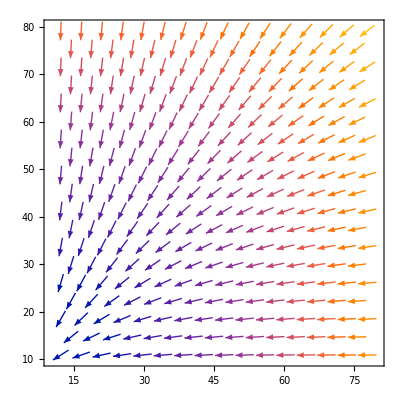

```mathematica
VectorPlot[{-x-x^2,-y-0.75y^2},{x,10,80},{y,10,80}]
```

```mathematica
Plot3D
```

```mathematica
currentPos={10,10};
timeTaken = 0;
onStarboard = 1;
possibleMoves[x_,y_]:=Module[{xpos=x,ypos=y},
Cases[liftCalcs,{Round[CubeRoot[Sqrt[(-x-x^2)^2+(-y-0.75y^2)^2]]],___,___,___}]
]
```

```mathematica
Round[CubeRoot[Sqrt[(-10-10^2)^2+(-10-0.75*10^2)^2]]]
```

5

```mathematica
possibleMoves[10,10]
```

{{5,0.,-52.5,12031.3},{5,0.,-50.,11129.5},{5,0.,-47.5,10462.4},{5,0.,-45.,9340.7},{5,0.,-42.5,8479.94},{5,0.,-40.,8070.49},{5,0.,-37.5,7690.91}}

```mathematica
currentPos[[2]]
```

15

```mathematica
ClearAll[bA,wA,wS];
currentPos={10,10};
move[x_,y_,sA_Real,bA_]:=Module[{windSpeed=Round[CubeRoot[Sqrt[(-x-x^2)^2+(-y-0.75y^2)^2]]],windAngle=ArcTan[(-y-0.75y^2),(-x-x^2)],sailAngle=sA,boatAngle=bA,liftMag},
liftMag=(Flatten[Cases[liftCalcs,{windSpeed,sailAngle,-boatAngle,___}]][[4]]);
{currentPos=Flatten[{If[Divisible[onStarboard,2],{currentPos[[1]]=currentPos[[1]]-(Cos[windAngle+(180+boatAngle)Degree])*5,currentPos[[2]]=currentPos[[2]]+(Sin[windAngle+(180+boatAngle)Degree])*5},{currentPos[[1]]=currentPos[[1]]+(Cos[windAngle+(180-boatAngle)Degree])*5,currentPos[[2]]=currentPos[[2]]+(Sin[windAngle+(180-boatAngle)Degree])*5}]}],timeTaken+=1000/Sqrt[liftMag]}
]
```

```mathematica
onStarboard = 2;
move[currentPos[[1]],currentPos[[2]],0.,42.5]
```

{{6.59018,24.1086},0.886345}

```mathematica
Flatten[Cases[liftCalcs,{5,0.,-42.5,___}]][[4]]
```

9250.98

```mathematica
currentPos[[1]]
```

10

```mathematica
ArcTan[(-10-0.75*10^2),(-10-10^2)]
```

-2.22868

```mathematica
windAngle
```

windAngle

1 =0.145
2=0.2905
3=0.43

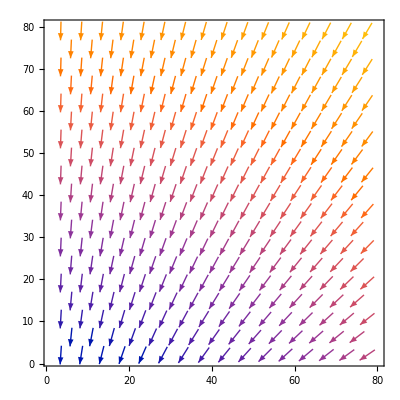

```mathematica
VectorPlot[{-x,-(y+50)},{x,1,80},{y,1,80}]
onStarboard=2;
currentPos={10,10};
goal={80,80};
```

```mathematica
Round[Sqrt[(-1)^2+(-(1+50))^2]/7]
ArcTan[(-(1+50)^2),((-1-1^2)^2)]
```

7

π-ArcTan[4/2601]

```mathematica
randomMove[x_,y_]:=Module[{choice},
If[x<10||y<10||x>80||y>80,onStarboard+=1;choice=RandomChoice[possibleMoves[x,y]];move[x,y,choice[[2]],-choice[[3]]],onStarboard=onStarboard+=RandomChoice[{0,1}];
choice=RandomChoice[possibleMoves[x,y]];move[x,y,choice[[2]],-choice[[3]]]]
]
```

```mathematica
Table[randomMove[currentPos[[1]],currentPos[[2]]],20]
```

{{{14.8851,11.0656},16.5124},{{16.3037,15.8602},25.8148},{{21.2023,16.8621},33.9193},{{25.9976,18.278},40.9988},{{30.3689,20.7052},47.6553},{{35.0602,22.4349},53.3641},{{39.1587,25.2989},59.4161},{{41.6349,29.6427},63.7956},{{43.4508,34.3013},68.4765},{{44.4997,39.19},73.3591},{{45.9643,43.9707},77.4238},{{50.9179,44.6504},81.5356},{{52.6098,49.3554},85.4228},{{53.1642,54.3246},90.2218},{{54.3974,59.1701},93.0835},{{54.9026,64.1445},96.369},{{59.8679,64.7327},99.8885},{{64.8392,65.268},103.46},{{66.1443,70.0946},105.788},{{71.1443,70.0759},108.45}}

```mathematica
fucl[]:=Module[{},
	Print["fuc"];
	21
];
```

```mathematica
fucl[]
```

fuc

21

```mathematica
SystemModeler[]
```

SystemModeler::ncor: System Modeler is a full graphical modeling and simulation environment available in the Wolfram System Modeler product.

```mathematica
Sqrt[(-10-10^2)^2+(-10-0.75*10^2)^2]
ArcTan[(-10-0.75*10^2),(-10-10^2)]
```

139.014

-2.22868

```mathematica
possibleMoves[15,15]
```

{{7,0.,-52.5,23401.8},{7,0.,-50.,21509.6},{7,0.,-47.5,20156.2},{7,0.,-45.,18067.8},{7,0.,-42.5,16450.1},{7,0.,-40.,15640.2},{7,0.,-37.5,14855.9}}

```mathematica
Cases[liftCalcs,{Round[CubeRoot[Sqrt[(-10-10^2)^2+(10-0.75*10^2)^2]]],___,___,___}]
```

{{5,0.,-37.5,7690.91},{5,0.,-40.,8070.49},{5,0.,-42.5,8479.94},{5,0.,-45.,9340.7},{5,0.,-47.5,10462.4},{5,0.,-50.,11129.5},{5,0.,-52.5,12031.3},{5,2.5,-37.5,6682.25},{5,2.5,-40.,7470.},{5,2.5,-42.5,7827.36},{5,2.5,-45.,8138.64},{5,2.5,-47.5,8822.38},{5,2.5,-50.,10031.9},{5,2.5,-52.5,10580.1},{5,5.,-37.5,6126.1},{5,5.,-40.,6819.55},{5,5.,-42.5,7611.},{5,5.,-45.,8210.88},{5,5.,-47.5,8706.91},{5,5.,-50.,9575.71},{5,5.,-52.5,10897.},{5,7.5,-37.5,5604.9},{5,7.5,-40.,6194.61},{5,7.5,-42.5,6979.7},{5,7.5,-45.,7945.85},{5,7.5,-47.5,8475.1},{5,7.5,-50.,8872.1},{5,7.5,-52.5,9797.},{5,10.,-37.5,5371.85},{5,10.,-40.,5746.39},{5,10.,-42.5,6289.6},{5,10.,-45.,7034.1},{5,10.,-47.5,7907.04},{5,10.,-50.,8388.26},{5,10.,-52.5,8610.39},{5,12.5,-37.5,5135.22},{5,12.5,-40.,5437.4},{5,12.5,-42.5,5816.49},{5,12.5,-45.,6388.05},{5,12.5,-47.5,7123.95},{5,12.5,-50.,7914.53},{5,12.5,-52.5,8274.36},{5,15.,-37.5,4640.49},{5,15.,-40.,5218.46},{5,15.,-42.5,5565.1},{5,15.,-45.,5885.},{5,15.,-47.5,6449.72},{5,15.,-50.,7212.97},{5,15.,-52.5,8075.01}}

```mathematica
binary search
```

```mathematica
Dynamic
```

```mathematica
Minimize
```

```mathematica
chooseMove[x_,y_,m_Integer]:=Module[{choice},
If[m<50,choice=possibleMoves[x,y][[m]];move[x,y,choice[[2]],-choice[[3]]],onStarboard+=1;timeTaken+=2;]
]
```

```mathematica
chooseMove[currentPos[[1]],currentPos[[2]],7]
```

{{28.6695,19.9861},85.3975}

```mathematica
Minimize[chooseMove[currentPos[[1]],currentPos[[2]],m][[2]],m]
```

{82.2248,{m→-12/5}}

```mathematica
testrun=DeleteCases[{{{15.005360640558585,19.999997126352454},96.65956623066299},{{14.084655778831248,24.914496343728693},93.69932289598279},{{11.847546507319926,29.386111500170276},91.93260962811912},{{9.552009876217031,33.828015548578435},89.50173046915762},"Tack",{{13.835431484098166,31.248810374665936},87.98540953529768},{{17.80459371682211,28.20812769304362},85.9458090361874},{{22.590644335535803,26.761158628028653},84.0971184507111},{{27.527485244048165,25.968945371361723},80.3270798506212},{{32.50103400010556,26.482572445336512},76.29558025169842},{{37.316933771117206,27.82686013611182},71.88380000298702},{{41.77416065927947,30.092500987492148},67.48593947546611},{{46.364656559027196,32.0742546034594},62.91995232377292},{{50.899879913765716,34.17942659705857},58.31531146071958},{{55.394402483694876,36.37014950705822},53.800989855885724},{{59.75571231458241,38.81534409215851},49.468772686987},{{64.10082416562406,41.289208074259655},45.196466295540525},{{68.80082852122153,42.99506828464174},41.32247000910202},{{72.84979308960382,45.92864731442511},38.129345759940385},{{77.03534321905283,48.66382009029675},34.48641565703327}},"Tack"];
```

```mathematica
First/@testrun
```

{{15.0054,20.},{14.0847,24.9145},{11.8475,29.3861},{9.55201,33.828},{13.8354,31.2488},{17.8046,28.2081},{22.5906,26.7612},{27.5275,25.9689},{32.501,26.4826},{37.3169,27.8269},{41.7742,30.0925},{46.3647,32.0743},{50.8999,34.1794},{55.3944,36.3701},{59.7557,38.8153},{64.1008,41.2892},{68.8008,42.9951},{72.8498,45.9286},{77.0353,48.6638}}

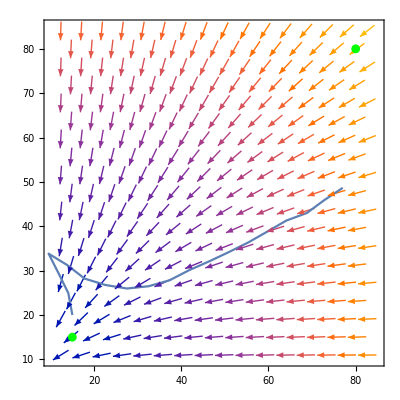

```mathematica
Show[VectorPlot[{windx,windy},{x,10,85},{y,10,85}],ListLinePlot[First/@testrun,Frame->True,PlotRange->{{10,85},{10,85}}],Graphics[{Directive[Green,EdgeForm[None]],Disk[{15,15},1]}],Graphics[{Directive[Green,EdgeForm[None]],Disk[{80,80},1]}]]
```

```mathematica
move[20,5,Map[#[[3]]&,possibleMoves[20,5]]]
```

Part::partw: Part 4 of {} does not exist.

{{34.5061,34.7126,34.9159,35.1156,35.3112,35.5024,35.6889,37.9758,37.9056,37.8265,37.7386,37.6421,37.5371,37.4238},51.9701+1000/(√({}⟦4⟧))}

```mathematica
possibleMoves[20,5]
```

{{8,0.,-52.5,31109.4},{8,0.,-50.,28270.4},{8,0.,-47.5,26284.6},{8,0.,-45.,23448.3},{8,0.,-42.5,21268.9},{8,0.,-40.,20169.1},{8,0.,-37.5,19125.2}}

```mathematica
#[[3]]&/@possibleMoves[20,5]
```

{-52.5,-50.,-47.5,-45.,-42.5,-40.,-37.5}

```mathematica
move[20,5,#&],{-52.5,-50.,-47.5,-45.,-42.5,-40.,-37.5}
```

Syntax::tsntxi: "move[20,5,#]&,{-52.5,-50.,-47.5,-45.,-42.5,-40.,-37.5}" is incomplete; more input is needed.

```mathematica
Map[move[20,5,-#]&,#[[3]]&/@possibleMoves[20,5]]
```

{{{24.2162,2.31226},5.66962},{{28.5456,-0.189018},11.6171},{{32.9799,-2.49907},17.7852},{{37.5108,-4.6135},24.3157},{{42.1297,-6.52827},31.1725},{{46.8276,-8.23976},38.2139},{{51.5958,-9.7447},45.4449}}

```mathematica
ArcTan[(-(5+50)),(-20.)]
```

```mathematica
-2.7928216500058864*180/Pi
```

-160.017

```mathematica
move[20,5,52.5]
```

{{18.4951,9.76814},5.66962}

```mathematica
{currentPos[[1]]-=(Cos[(-160+180+52.5)Degree])*5,currentPos[[2]]+=(Sin[(-160+180+52.5)Degree])*5},{currentPos[[1]]+=(Cos[(-160+180-52.5)Degree])*5,currentPos[[2]]+=(Sin[(-160+180-52.5)Degree])*5}
```

Syntax::tsntxi: "{currentPos[[1]]-=(Cos[(-160+180+52.5)Degree])*5,currentPos[[2]]+=(Sin[(-160+180+52.5)Degree])*5},{currentPos[[1]]+=(Cos[(-160+180-52.5)Degree])*5,currentPos[[2]]+=(Sin[(-160+180-52.5)«6»])*5}" is incomplete; more input is needed.

```mathematica
(Cos[(-160+180+52.5)Degree])*5
```

1.50353

```mathematica
Round[Sqrt[(-20)^2+(-(5+50))^2]/7]
```

8

```mathematica
Flatten[Cases[liftCalcs,{8,___,-50.,___}]][[4]]
```

28270.4

```mathematica
Cases[liftCalcs,{8,___,-50.,___}]
```

{{8,0.,-50.,28270.4}}

```mathematica
move[20,5,50]
```

Part::partw: Part 4 of {} does not exist.

{{149.756-10 Cos[ArcTan[4/11]+° (180+52.5 (#1&))]-5 Cos[ArcTan[4/11]+° (180-#1)],191.966-5 Cos[ArcTan[4/11]+° (180+50. (#1&))]-5 Cos[ArcTan[4/11]+° (180+52.5 (#1&))]-5 Sin[ArcTan[4/11]+° (180-#1)]},11.895+5000/(√({}⟦4⟧))+√((-66.3972+10 Cos[ArcTan[4/11]+° (180+52.5 (#1&))]+5 Cos[ArcTan[4/11]+° (180-#1)])^2+(-119.774+5 Cos[ArcTan[4/11]+° (180+50. (#1&))]+5 Cos[ArcTan[4/11]+° (180+52.5 (#1&))]+5 Sin[ArcTan[4/11]+° (180-#1)])^2)}

```mathematica
move[20,5,-50]
```

Part::partw: Part 4 of {} does not exist.

{{128.109-10 Cos[ArcTan[4/11]+° (180+52.5 (#1&))]-5 Cos[ArcTan[4/11]+° (180-#1)],204.472-5 Cos[ArcTan[4/11]+° (180+50. (#1&))]-5 Cos[ArcTan[4/11]+° (180+52.5 (#1&))]-5 Sin[ArcTan[4/11]+° (180-#1)]},2000/(√({}⟦4⟧))+√((-66.3972+10 Cos[ArcTan[4/11]+° (180+52.5 (#1&))]+5 Cos[ArcTan[4/11]+° (180-#1)])^2+(-119.774+5 Cos[ArcTan[4/11]+° (180+50. (#1&))]+5 Cos[ArcTan[4/11]+° (180+52.5 (#1&))]+5 Sin[ArcTan[4/11]+° (180-#1)])^2)}

put each value of the list #[[3]]&/@possibleMoves[20,5] into the slot and run the function move for each value

{-52.5 (move[20,5,#1]&),-50. (move[20,5,#1]&),-47.5 (move[20,5,#1]&),-45. (move[20,5,#1]&),-42.5 (move[20,5,#1]&),-40. (move[20,5,#1]&),-37.5 (move[20,5,#1]&)}

```mathematica
{20,5,#&Map[#[[3]]&,possibleMoves[20,5]]}
```

{20,5,{-52.5 (#1&),-50. (#1&),-47.5 (#1&),-45. (#1&),-42.5 (#1&),-40. (#1&),-37.5 (#1&)}}

```mathematica
move[20,5,#&,#[[3]]&@@@possibleMoves[20,5]]
```

Part::partd: Part specification 8⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
1+1
```

2

```mathematica
%*2
```

{{{-2.45955,90.23},152.28,2},{{-2.87265,90.0897},153.264,4},{{-3.27924,89.9314},154.137,6},{{-3.67853,89.7556},155.295,8},{{-4.06978,89.5625},156.384,10},{{-4.45223,89.3525},157.189,12},{{-4.82516,89.1261},158.004,14},{{8.98265,75.3183},150.967,16},{{9.2091,75.6912},151.116,18},{{9.41907,76.0736},151.159,20},{{9.61215,76.4649},151.494,22},{{9.78799,76.8642},151.765,24},{{9.94624,77.2708},151.763,26},{{10.0866,77.6839},151.782,28}}

```mathematica
evalAllMoves[20,5]
```

{{{-1.22977,45.115},76.1398,1},{{-1.43633,45.0448},76.6319,2},{{-1.63962,44.9657},77.0683,3},{{-1.83927,44.8778},77.6477,4},{{-2.03489,44.7812},78.1919,5},{{-2.22612,44.6763},78.5945,6},{{-2.41258,44.563},79.0022,7},{{4.49133,37.6591},75.4834,8},{{4.60455,37.8456},75.5582,9},{{4.70953,38.0368},75.5795,10},{{4.80608,38.2324},75.7468,11},{{4.89399,38.4321},75.8827,12},{{4.97312,38.6354},75.8817,13},{{5.0433,38.8419},75.8912,14}}

```mathematica
Names["Global`*"]
```

{a,all,answer,AOA,AOA$$,a$,a$$,b,bA,bAngle,bAngle$,bAngle$130582,best,BitDepth,boatAngle,boatAngle$,boatAngle$1584534,boatAngle$1585212,boatAngle$1588575,boatAngle$1588907,boatAngle$1589242,boatAngle$1591668,boatAngle$1592660,boatAngle$1594372,boatAngle$1596505,boatAngle$1598729,boatAngle$2547475,boatAngle$2547868,boatAngle$2549153,boatAngle$2549772,boatAngle$2550767,boatAngle$2607486,boatAngle$2663400,boatAngle$74014396,boatAngle$74722318,boatAngle$81044215,boatAngle$84744814,boatAngle$85888125,boatAngle$92195598,boatAngle$96620754,boatAngle$96620786,boatAngle$96620795,boatAngle$96620892,boatAngle$96620895,boatAngle$96620898,boatAngle$96620989,boatAngle$96620992,boatAngle$96620995,boatAngle$96621042,boatAngle$96626699,boatAngle$96628104,boatAngle$96628107,boatAngle$96628110,boatAngle$96628162,boatAngle$96628165,boatAngle$96628168,boatAngle$96628193,boatAngle$96628355,boatAngle$96628358,boatAngle$96628361,boatAngle$96628379,boatAngle$96628382,boatAngle$96628385,boatAngle$96628424,boatAngle$96628432,boatAngle$96628465,boatAngle$96628473,boatAngle$96628481,boatAngle$96628497,boatAngle$96628689,boatAngle$96628692,boatAngle$96628695,boatAngle$96628786,boatAngle$96628795,boatAngle$96628802,boatAngle$96628813,boatAngle$96628864,b$,b$$,cc,cdata,CFloat,choice,choices,choices$,choicetest,choice$,choice$1644009,choice$1644025,choice$1644041,choice$1644057,choice$1644612,choice$1644621,choice$1644630,choice$1644907,choice$1644916,choice$1644925,choice$1645238,choice$1645257,choice$1647609,choice$1647618,choice$1647627,choice$1647868,choice$1647877,choice$1647886,choice$1648634,choice$1648643,choice$1648652,choice$1649337,choice$1649346,choice$1649355,choice$1649590,choice$1649599,choice$1649608,choice$2397876,choice$2397885,choice$2397894,choice$2397958,choice$2397967,choice$2397976,choice$2398046,choice$2398055,choice$2398064,choice$2445099,choice$2445108,choice$2445117,choice$2445187,choice$2445196,choice$2445205,choice$2445245,choice$2445270,choice$2448253,choice$2448262,choice$2448271,choice$2448357,choice$2448366,choice$2448375,choice$2448456,choice$2448465,choice$2448474,choice$2449001,choice$2449010,choice$2449019,choice$2449092,choice$2449101,choice$2449110,choice$2449410,choice$2449419,choice$2449428,choice$2451191,choice$2451200,choice$2451209,choice$2451399,choice$2451408,choice$2451417,choice$2454947,choice$2454956,choice$2454965,choice$2455232,choice$2455241,choice$2455250,choice$2466532,choice$2466541,choice$2466693,choice$2480072,choice$2501590,choice$2506070,choice$2506566,choice$2509378,choice$2511778,choice$2514165,choice$2523299,choice$2523743,choice$2523782,choice$2529442,choice$2529458,choice$2534922,choice$2535146,choice$2535218,choice$2535336,choice$2535665,choice$2535691,choice$2536080,choice$2536096,choice$2537742,choice$2537749,choice$2537976,choice$2537983,choice$2538267,choice$2538274,choice$2538679,choice$2538686,choice$2547469,choice$2547862,choice$2549147,choice$2549766,choice$2550761,choice$2607480,choice$2663394,choice$74014390,choice$74722312,choice$81044209,choice$84744808,choice$85888119,choice$92195592,chooseMove,chooseMoveMove,Cl,cMinMax,cname,colors,crange,currentPos,distanceFromGoal,Emit,evalNextMove,f,fucl,FullScreenArea,genAll,goal,h,height,height$,h$,InterpolatingIrregularFunction,ja,jAOA,jAOA$$,ja$$,jb,jb$$,jCl,jf,jL,jmat,jobjs,jpp,jpsol,jpts,jt,L,liftCalcs,liftMag,liftMag$,liftMag$1584534,liftMag$1585212,liftMag$1588575,liftMag$1588907,liftMag$1589242,liftMag$1591668,liftMag$1592660,liftMag$1594372,liftMag$1596505,liftMag$1598729,liftMag$2547475,liftMag$2547868,liftMag$2549153,liftMag$2549772,liftMag$2550767,liftMag$2607486,liftMag$2663400,liftMag$74014396,liftMag$74722318,liftMag$81044215,liftMag$84744814,liftMag$85888125,liftMag$92195598,liftMag$96620754,liftMag$96620786,liftMag$96620795,liftMag$96620892,liftMag$96620895,liftMag$96620898,liftMag$96620989,liftMag$96620992,liftMag$96620995,liftMag$96621042,liftMag$96626699,liftMag$96628104,liftMag$96628107,liftMag$96628110,liftMag$96628162,liftMag$96628165,liftMag$96628168,liftMag$96628193,liftMag$96628355,liftMag$96628358,liftMag$96628361,liftMag$96628379,liftMag$96628382,liftMag$96628385,liftMag$96628424,liftMag$96628432,liftMag$96628465,liftMag$96628473,liftMag$96628481,liftMag$96628497,liftMag$96628689,liftMag$96628692,liftMag$96628695,liftMag$96628786,liftMag$96628795,liftMag$96628802,liftMag$96628813,liftMag$96628864,locationFunc,L$,m,Mag,mat,mL,mouseUp$$,move,negatives,nextDateFunc,noncommittal,objs,onStarboard,plotBest,pos,positives,possibleMoves,pp,prevDateFunc,psol,pts,querystate40,querystate41,querystate42,querystate43,question,randomMove,Resolution,Riff,s,sA,sailAngle,sailAngle$,sailAngle$1584534,sailAngle$1585212,sailAngle$1588575,sailAngle$1588907,sailAngle$1589242,sailAngle$1591668,sailAngle$1592660,sailAngle$1594372,sailAngle$1596505,sailAngle$1598729,sailReset,sAngle,sAngle$,sAngle$130582,score,ScreenArea,sinx,state,StereoView,s$,t,tackTimes,testrun,timeTaken,t$,ucoords,usol,uvcoords,vcoords,ViewSize,vort,vsol,w,wA,width,width$,wind,windAngle,windAngle$,windAngle$1584534,windAngle$1585212,windAngle$1588575,windAngle$1588907,windAngle$1589242,windAngle$1591668,windAngle$1592660,windAngle$1594372,windAngle$1596505,windAngle$1598729,windAngle$2547475,windAngle$2547868,windAngle$2549153,windAngle$2549772,windAngle$2550767,windAngle$2607486,windAngle$2663400,windAngle$74014396,windAngle$74722318,windAngle$81044215,windAngle$84744814,windAngle$85888125,windAngle$92195598,windAngle$96620754,windAngle$96620786,windAngle$96620795,windAngle$96620892,windAngle$96620895,windAngle$96620898,windAngle$96620989,windAngle$96620992,windAngle$96620995,windAngle$96621042,windAngle$96626699,windAngle$96628104,windAngle$96628107,windAngle$96628110,windAngle$96628162,windAngle$96628165,windAngle$96628168,windAngle$96628193,windAngle$96628355,windAngle$96628358,windAngle$96628361,windAngle$96628379,windAngle$96628382,windAngle$96628385,windAngle$96628424,windAngle$96628432,windAngle$96628465,windAngle$96628473,windAngle$96628481,windAngle$96628497,windAngle$96628689,windAngle$96628692,windAngle$96628695,windAngle$96628786,windAngle$96628795,windAngle$96628802,windAngle$96628813,windAngle$96628864,windSpeed,windSpeed$,windSpeed$1584534,windSpeed$1585212,windSpeed$1588575,windSpeed$1588907,windSpeed$1589242,windSpeed$1591668,windSpeed$1592660,windSpeed$1594372,windSpeed$1596505,windSpeed$1598729,windSpeed$2547475,windSpeed$2547868,windSpeed$2549153,windSpeed$2549772,windSpeed$2550767,windSpeed$2607486,windSpeed$2663400,windSpeed$74014396,windSpeed$74722318,windSpeed$81044215,windSpeed$84744814,windSpeed$85888125,windSpeed$92195598,windSpeed$96620754,windSpeed$96620786,windSpeed$96620795,windSpeed$96620892,windSpeed$96620895,windSpeed$96620898,windSpeed$96620989,windSpeed$96620992,windSpeed$96620995,windSpeed$96621042,windSpeed$96626699,windSpeed$96628104,windSpeed$96628107,windSpeed$96628110,windSpeed$96628162,windSpeed$96628165,windSpeed$96628168,windSpeed$96628193,windSpeed$96628355,windSpeed$96628358,windSpeed$96628361,windSpeed$96628379,windSpeed$96628382,windSpeed$96628385,windSpeed$96628424,windSpeed$96628432,windSpeed$96628465,windSpeed$96628473,windSpeed$96628481,windSpeed$96628497,windSpeed$96628689,windSpeed$96628692,windSpeed$96628695,windSpeed$96628786,windSpeed$96628795,windSpeed$96628802,windSpeed$96628813,windSpeed$96628864,windx,windy,wind$,wind$130582,wS,w$,x,x1,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x2,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29,x3,x30,x31,x32,x33,x34,x35,x36,x37,x38,x39,x4,x40,x41,x42,x43,x44,x45,x46,x47,x48,x49,x5,x50,x51,x52,x53,x54,x55,x56,x57,x58,x59,x6,x60,x61,x62,x63,x64,x65,x66,x67,x68,x69,x7,x70,x71,x72,x73,x74,x75,x76,x77,x78,x79,x8,x80,x9,xpos,xpos$,x$,y,ypos,ypos$,y$,z}

```mathematica
randomMove[20,5]
```

Part::partw: Part 3 of {{24.5309,2.88557},6.53047} does not exist.

{{{24.5309,2.88557},6.53047},{{24.5309,2.88557},6.53047}⟦3⟧}

```mathematica
all=Table[sailReset[];{Table[randomMove[currentPos[[1]],currentPos[[2]]],30],score+=(timeTaken+distanceFromGoal);score},1000];
best=SortBy[all,#[[-1]]&][[1]];
plotBest=Flatten[Drop[#,-1]&/@Insert[First/@DeleteCases[Flatten[Drop[best,-1],1],"Tack"],{{20.,5.},0},1],1]
```

{{20.,5.},{18.4951,9.76814},{16.557,14.3773},{20.493,11.2937},{24.8655,8.86864},{29.704,7.60818},{34.2273,5.47744},{38.9737,3.90523},{43.8223,2.68436},{48.6991,1.58116},{53.6655,1.00247},{58.6045,1.78097},{63.5768,2.30685},{68.5533,2.79083},{69.6271,7.67417},{70.7403,12.5487},{71.047,17.5393},{71.1735,22.5377},{70.4739,27.4885},{70.891,32.471},{70.7324,37.4685},{70.8599,42.4669},{70.2041,47.4237},{70.0538,52.4214},{68.7067,57.2366},{68.2838,62.2187},{66.8905,67.0206},{65.3665,71.7827},{63.7159,76.5024}}

```mathematica
{Table[randomMove[currentPos[[1]],currentPos[[2]]],30],score+=(timeTaken+distanceFromGoal);score}
```

{{{{{24.5309,2.88557},6.53047},-45.},{{{29.2965,1.37241},13.3874},-42.5},Tack,{{{27.3585,5.98156},20.6183},-37.5},{{{25.131,10.458},27.0444},-37.5},{{{23.8429,15.2892},32.054},-52.5},{{{22.3445,20.0594},36.5423},-52.5},{{{19.4902,24.1646},41.7574},-37.5},{{{17.1602,28.5885},46.2329},-47.5},{{{13.934,32.4085},51.448},-37.5},{{{11.5942,36.8272},55.1488},-52.5},{{{8.38729,40.6634},59.3259},-42.5},{{{5.02775,44.3665},63.503},-42.5},{{{2.02214,48.3623},66.8309},-50.},{{{-1.88123,51.487},70.8029},-37.5},Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack},170.937}

```mathematica
best
```

{{{{{24.5309,2.88557},6.53047},-45.},{{{28.9613,0.567869},12.2001},-52.5},Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack,Tack},153.481}

```mathematica
chooseMove[20,5,7]
```

{{{24.7681,3.49507},7.23097},-37.5}

```mathematica
evalAllMoves[20,5]
```

{{{18.4951,9.76814},5.66962,87.2489,1},{{18.2885,9.69796},5.9475,87.6924,2},{{18.0852,9.61883},6.16807,88.0848,3},{{17.8856,9.53092},6.53047,88.625,4},{{17.6899,9.43437},6.85689,89.1348,5},{{17.4987,9.32939},7.04137,89.5077,6},{{17.3123,9.21616},7.23097,89.8905,7},{{24.2162,2.31226},5.66962,91.2025,8},{{24.3294,2.49872},5.9475,91.2636,9},{{24.4344,2.68995},6.16807,91.2666,10},{{24.5309,2.88557},6.53047,91.4109,11},{{24.6188,3.08522},6.85689,91.5192,12},{{24.698,3.28851},7.04137,91.4859,13},{{24.7681,3.49507},7.23097,91.4586,14}}

```mathematica
best=SortBy[evalAllMoves[20,5],#[[-2]]&][[1]]
```

{{18.4951,9.76814},5.66962,87.2489,1}

```mathematica
best[[4]]
```

1

```mathematica
CloudPut[NotebookOpen["/Users/ethan.k/Desktop/CodingNStuff/Wolfram/Project/WindTunnel2DLBM/WindTunnel2DLBM.m"],"WindTunnelPackage"]
```

CloudObject[https://www.wolframcloud.com/obj/ethankong0209/WindTunnelPackage]

```mathematica
CloudImport[CloudObject[["https://www.wolframcloud.com/obj/ethankong0209/WindTunnelPackage"](https://www.wolframcloud.com/obj/ethankong0209/WindTunnelPackage)]]
```

```mathematica
Get["/Users/ethan.k/Desktop/CodingNStuff/Wolfram/Project/WindTunnel2DLBM/WindTunnel2DLBM.m"]
```

```mathematica
possibleMoves[20,5]
```

{}

```mathematica
Cases[liftCalcs,{Round[Sqrt[(-20)^2+(-(5+50))^2]/7],___,___,___}]
```

{}

```mathematica
Round[Sqrt[(-20)^2+(-(5+50))^2]/7]
```

8

```mathematica
Cases[liftCalcs,{8.,___,___,___}]
```

{{8.,0.,-52.5,31109.4},{8.,0.,-50.,28270.4},{8.,0.,-47.5,26284.6},{8.,0.,-45.,23448.3},{8.,0.,-42.5,21268.9},{8.,0.,-40.,20169.1},{8.,0.,-37.5,19125.2}}

```mathematica
evalAllMoves[20,5]
```

{{{63.1876,79.2583},5.66962,3.27274,1},{{63.3008,79.4447},5.9475,3.34719,2},{{63.4058,79.6359},6.16807,3.42519,3},{{63.5023,79.8316},6.53047,3.50638,4},{{63.5902,80.0312},6.85689,3.59038,5},{{63.6694,80.2345},7.04137,3.67686,6},{{63.7396,80.4411},7.23097,3.76548,7},{{57.4665,86.7141},5.66962,7.17624,8},{{57.2599,86.644},5.9475,7.1868,9},{{57.0566,86.5648},6.16807,7.19447,10},{{56.857,86.4769},6.53047,7.19923,11},{{56.6614,86.3804},6.85689,7.20108,12},{{56.4701,86.2754},7.04137,7.20003,13},{{56.2837,86.1622},7.23097,7.19606,14}}

```mathematica
best=SortBy[evalAllMoves[20,5],#[[-1]]&][[1]]
```

{{24.2162,2.31226},5.66962,85.5328,1}